```mathematica
InNodes[g_,v_]:=Map[First,Select[EdgeList[g],(#[[2]] == v)&]]
```

```mathematica
OutNodes[g_,v_]:=Block[{out=VertexOutComponent[g,{v}]},Select[out,#≠v&]]
```

```mathematica
Select[VertexList[VertexOutComponent[g,v]],#≠v&]
```

```mathematica
MobiusMatrix[g_]:=Block[{vertices=VertexList[g], zero, result=Association[], todo,current, outNodes, out},
Table[result[v]=0,{v,vertices}];
zero=First[Select[vertices,VertexOutDegree[g,#]==0&]];
result[zero]=1;
todo=InNodes[g,zero];
While[todo≠{},
current=First[todo];
todo=Rest[todo];
out=OutNodes[g,current];
result[current]=-Total[Table[result[v],{v,out}]];
todo=Join[todo,InNodes[g,current]]
];
result
]
```

```mathematica
MobiusMatrix[gg]
```

<|{{1},{1},{1},{1},{1}}→0,{{5}}→1,{{2},{1},{1},{1}}→-1,{{2},{2},{1}}→1,{{3},{1},{1}}→1,{{3},{2}}→-1,{{4},{1}}→-1|>

```mathematica
ToLabels[assoc_]:=Table[key->Rotate[Column[{Row[key],Style[assoc[key],Bold,Red]}],Pi/6],{key,Keys[assoc]}]
```

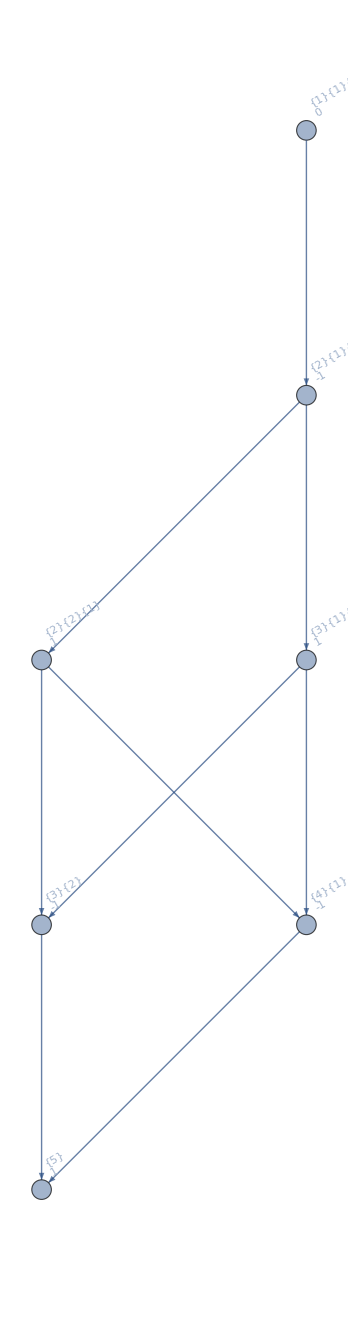

```mathematica
Graph[EdgeList[gg],VertexLabels->ToLabels[MobiusMatrix[gg]]]
```

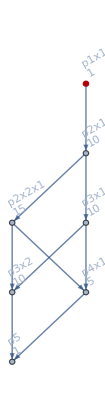
```mathematica
gg=-Graphics-;
```

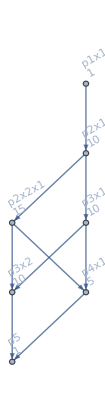

```mathematica
PartitionTypeLattice3[PartitionTypeFormula[allGraphs5[0,"graph"]]]
```

```mathematica
MobiusMatrix[%]
```

<|{{1},{1},{1},{1},{1}}→0,{{5}}→1,{{2},{1},{1},{1}}→-1,{{2},{2},{1}}→1,{{3},{1},{1}}→1,{{3},{2}}→-1,{{4},{1}}→-1|>

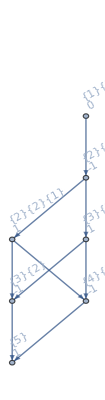

```mathematica
With[{ggg=PartitionTypeLattice3[PartitionTypeFormula[allGraphs5[0,"graph"]]]},
Graph[EdgeList[ggg],VertexLabels->ToLabels[MobiusMatrix[ggg]], GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
PartitionTypeLattice[IntegerPartitions[3]]
```

{{2,1}->{3},{1,1,1}->{2,1}}

```mathematica
ToLabels2[assoc_]:=Table[key->Rotate[Column[{ExponentNotation[key],Style[assoc[key],Bold,Red]}],Pi/6],{key,Keys[assoc]}]
```

```mathematica
ExponentNotation[{1,1,1}]
```

1^3

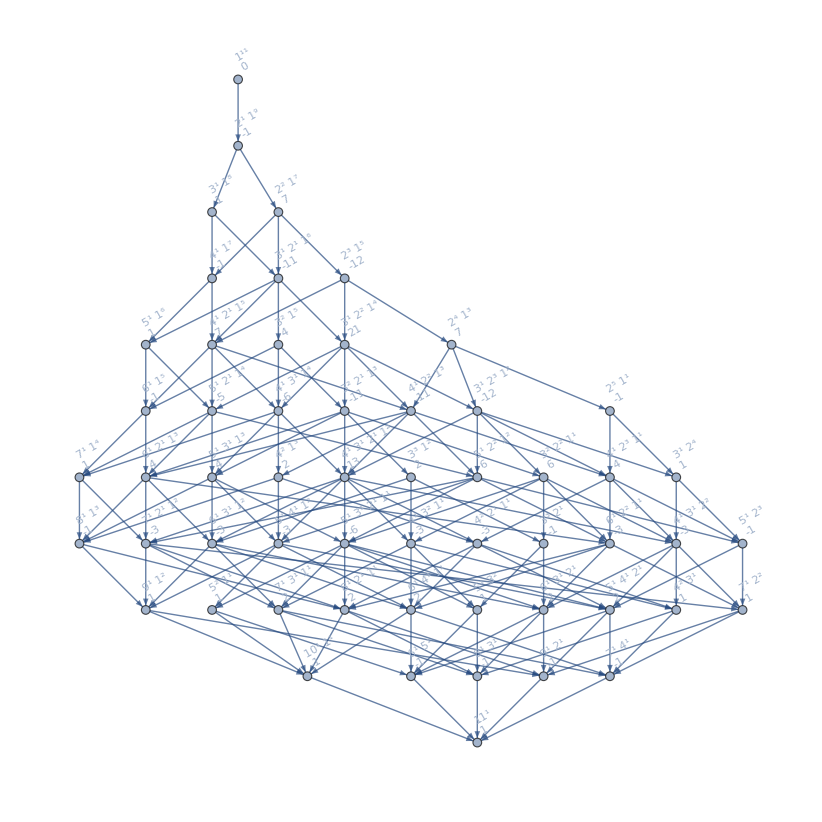

```mathematica
With[{ggg=PartitionTypeLattice[IntegerPartitions[11]]},
Graph[EdgeList[ggg],VertexLabels->ToLabels2[MobiusMatrix[ggg]],GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
VertexList[ReverseGraph[PartitionTypeLattice[IntegerPartitions[11]]]]
```

{{10,1},{11},{9,2},{8,3},{7,4},{6,5},{9,1,1},{8,2,1},{7,3,1},{6,4,1},{5,5,1},{7,2,2},{6,3,2},{5,4,2},{8,1,1,1},{7,2,1,1},{6,3,1,1},{5,4,1,1},{5,3,3},{4,4,3},{6,2,2,1},{5,3,2,1},{4,4,2,1},{7,1,1,1,1},{6,2,1,1,1},{5,3,1,1,1},{4,4,1,1,1},{4,3,3,1},{5,2,2,2},{4,3,2,2},{5,2,2,1,1},{4,3,2,1,1},{6,1,1,1,1,1},{5,2,1,1,1,1},{4,3,1,1,1,1},{3,3,3,2},{3,3,3,1,1},{4,2,2,2,1},{3,3,2,2,1},{4,2,2,1,1,1},{3,3,2,1,1,1},{5,1,1,1,1,1,1},{4,2,1,1,1,1,1},{3,3,1,1,1,1,1},{3,2,2,2,2},{3,2,2,2,1,1},{3,2,2,1,1,1,1},{4,1,1,1,1,1,1,1},{3,2,1,1,1,1,1,1},{2,2,2,2,2,1},{2,2,2,2,1,1,1},{2,2,2,1,1,1,1,1},{3,1,1,1,1,1,1,1,1},{2,2,1,1,1,1,1,1,1},{2,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1}}

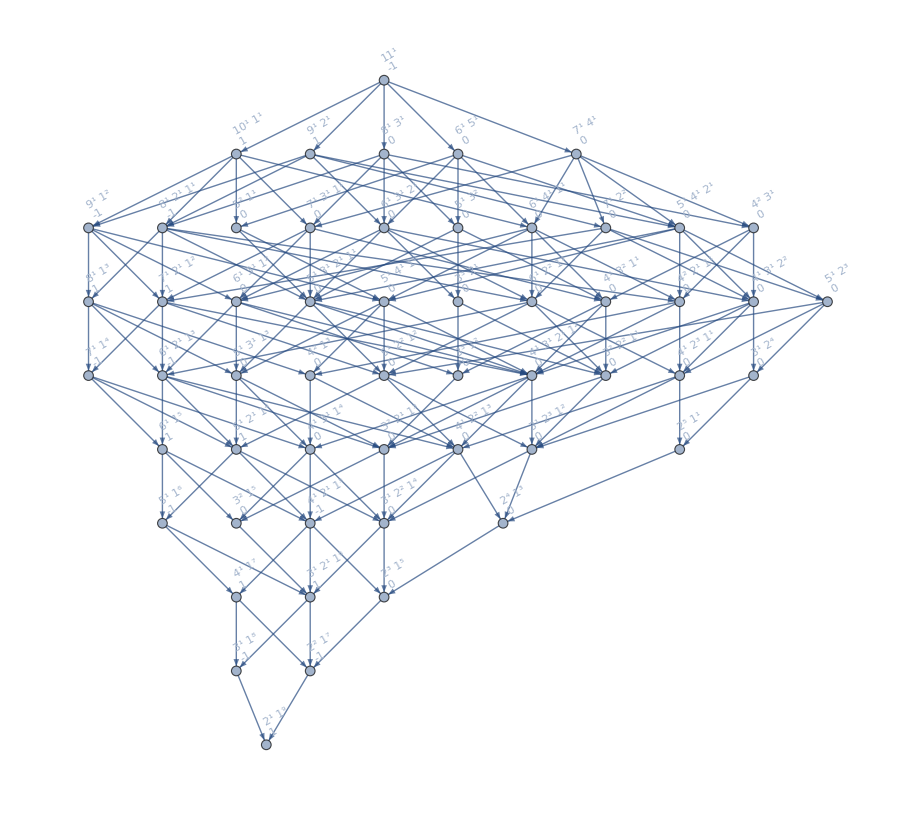

```mathematica
With[{ggg=VertexDelete[ReverseGraph[PartitionTypeLattice[IntegerPartitions[11]]],{1,1,1,1,1,1,1,1,1,1,1}]},
Graph[EdgeList[ggg],VertexLabels->ToLabels2[MobiusMatrix[ggg]],GraphLayout->"LayeredDigraphEmbedding"]
]
```